```mathematica
f[x_] = s (2-x)+1.7 x^8/(1+x^8)-x;
p1a=ContourPlot[Piecewise[{{f[x],f'[x]<0}},Indeterminate]==0,{s,0,1},{x,0,2},Frame->None,Axes->True,AxesLabel->{s,x},LabelStyle->Medium,ContourStyle->Thickness[0.015],AxesStyle->Thick,Ticks->{{-1,0,1,2}}];
p1b=ContourPlot[Piecewise[{{f[x],f'[x]>0}},Indeterminate]==0,{s,0,1},{x,0,2},Frame->None,Axes->True,AxesLabel->{s,x},LabelStyle->Medium,ContourStyle->{Dotted,Thickness[0.007]},AxesStyle->Thick,Ticks->{{-1,0,1,2}}];
```

```mathematica
g[x_] = s (2-x)+r x^8/(1+x^8)-x;
rs = Solve[{g[x]==0,g'[x]==0},{r,s}][[1]]
```

{r→(2 (1+2 x^8+x^16))/(x^7 (16-7 x+x^9)),s→-(-7 x+x^9)/(16-7 x+x^9)}

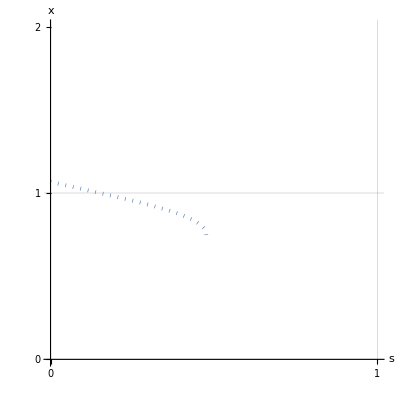

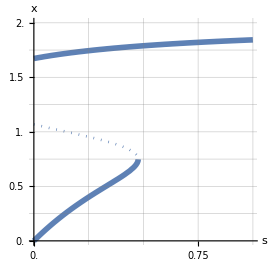

```mathematica
f[x_] = s (2-x)+1.7 x^8/(1+x^8)-x;
p1a=ContourPlot[Piecewise[{{f[x],f'[x]<0}},Indeterminate]==0,{s,0,1},{x,0,2},Frame->None,Axes->True,AxesLabel->{s,x},LabelStyle->Medium,ContourStyle->Thickness[0.015],AxesStyle->Thick,Ticks->{Table[val,{val,0,2,0.25}]},GridLines->{Table[val,{val,0,1,0.25}], Table[val,{val,0,2,0.25}]}];
p1b=ContourPlot[Piecewise[{{f[x],f'[x]>0}},Indeterminate]==0,{s,0,1},{x,0,2},Frame->None,Axes->True,AxesLabel->{s,x},LabelStyle->Medium,ContourStyle->{Dotted,Thickness[0.007]},AxesStyle->Thick,Ticks->{{-1,0,1,2}},GridLines->{{-1,0,1}, {-1,0,1}}]
Show[p1a,p1b]
```

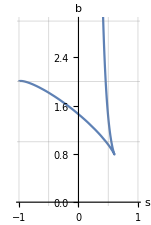

```mathematica
ParametricPlot[{s/.rs,r/.rs},{x,0.1,7},AxesLabel->{s,b},LabelStyle->Medium,PlotRange->{{-1,1},{0,3}},GridLines->{{-1,-0.5,0,0.5,1}, {-1,0,1,2,3}}]
```

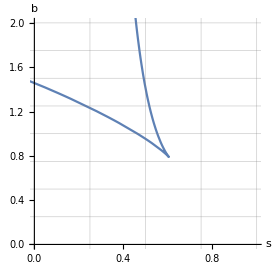

```mathematica
ParametricPlot[{s/.rs,r/.rs},{x,0.1,7},AxesLabel->{s,b},LabelStyle->Medium,PlotRange->{{0,1},{0,2}},GridLines->{Table[val,{val,0,2,0.25}],Table[val,{val,0,3,0.25}]},AspectRatio->1]
```